# ランダムサーファーモデル

ランダムサーファーモデルとは、Google PageRankの計算に用いられる考え方あるいはテクニックのひとつです。Googleの創始者である、ページとブリンが、主に計算上の問題を解決するために導入しました。
※数学的な説明: http://www.geocities.jp/existenzueda/random.htm

下図では、その考え方を概説します。

## Nav: top

## アニメーションによる説明:

以上webコンテンツ

## プログラム

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

```mathematica
MtoH[m_]:=Map[If[Tr[#]==0,#,#/Tr[#]]&,m]
```

```mathematica
MtoS[m_]:=Module[{l},
l=Dimensions[m][[2]];
Map[If[Tr[#]==0,Table[1/l,{l}],#/Tr[#]]&,m]
]
```

```mathematica
StoG[m_,a_]:=m*a+(1-a)/Length[m]
```

```mathematica
MtoG[m_,a_]:=MtoS[m]*a+(1-a)/Length[m]
```

```mathematica
nextScore[score_,m_]:=Map[Tr[#]&,Transpose[m*score]]
```

```mathematica
zeroSelf[mat_]:=ReplacePart[mat,Table[{n,n}->0,{n,Length[mat]}]]
```

## 定義と例示

```mathematica
l={{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
vnames["l"]=Table[IntegerString[n,"Roman"],{n,Length[l]}]
```

{I,II,III,IV,V,VI,VII,VIII}

```mathematica
vlabels["l"]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,Length[l]}]
```

{1→I,2→II,3→III,4→IV,5→V,6→VI,7→VII,8→VIII}

### スライド1

```mathematica
tb["l"]=TableForm[l,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,3.4}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0

```mathematica
gr["l"]=AdjacencyGraph[l,VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],ImagePadding->{{10,60},{10,20}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
txt["l"]=Graphics[{FontSize->16,Text[Style["左上: 基となるネットワーク
- 各点は各ページを表す。
リンクを矢印で表している。
たとえば、ページIは、ページ
IIIを参照し、ページVIIから
参照されている。

左下: その結合行列
- 行を見ると各ページへの
参照のリスト、列を見ると
各ページからの被参照の
リストである。

リンクの重みはすべて1である。",TextAlignment->Left]]},ImageSize->{250,380}];
```

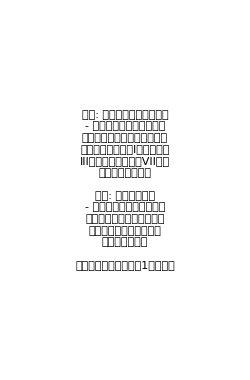
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 |

```mathematica
slide[1]=Grid[{{gr["l"],txt["l"]},{tb["l"],SpanFromAbove}},Alignment->{{Center,Center},{Top,Bottom}}]
```

### スライド2

```mathematica
txt[2]=Graphics[{FontSize->16,Text[Style["左上・左下: 前のスライドと同じ

このまま、\"ページランク\"
を計算すると、0点のページが
できてしまう。また、実際の
webではそのような0点のペー
ジがたくさんできてしまい、
一部のページしかランキング
に参加できなくなる。

そこで、計算上ではすべての
ページをリンクさせ、この問題
を回避するとともに実際的な
解釈を与える。",TextAlignment->Left]]},ImageSize->{250,430}];
```

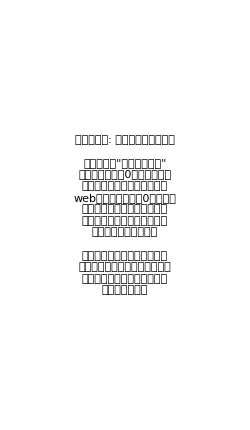
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 |

```mathematica
slide[2]=Grid[{{gr["l"],txt[2]},{tb["l"],SpanFromAbove}},Alignment->{{Center,Center},{Top,Bottom}}]
```

### スライド3

```mathematica
l
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
m=MtoH[l]
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1/3,1/3,1/3,0,0,0,0}}

```mathematica
tb["m"]=TableForm[m,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,3.4}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0

```mathematica
edgeforce["m"]=MapIndexed[If[#>0,{#2,#1}]&,m,{2}];
```

```mathematica
style["m"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/75])&,Cases[edgeforce["m"],_List,{2}]];
```

```mathematica
gr["m"]=AdjacencyGraph[toAdjacency[m],VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["m"],ImagePadding->{{10,60},{10,20}},ImageSize->{320,320}]
```

-Graphics-

```mathematica
txt["m"]=Graphics[{FontSize->16,Text[Style["左上: リンクに重みが
加わったネットワーク

左下: その結合行列

ランダムサーファーモデル
導入の第1段階として、各
ページが持つ配分できる点数
を、合計で1点とする。やがて
繰り返し計算によりこの点数
は変化する。これは、計算
のための初期値の設定。",TextAlignment->Left]]},ImageSize->{250,340}];
```

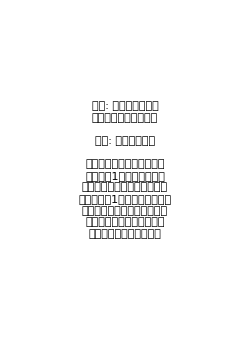
-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 |

```mathematica
slide[3]=Grid[{{gr["m"],txt["m"]},{tb["m"],SpanFromAbove}},Alignment->{{Center,Center},{Top,Bottom}}]
```

### スライド4

```mathematica
l
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
s=MtoS[l]
```

{{0,0,1,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},{0,1,0,0,0,0,0,0},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1/3,1/3,1/3,0,0,0,0}}

```mathematica
tb["s"]=TableForm[s,TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,3.4}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0

```mathematica
edgeforce["s"]=MapIndexed[If[#>0,{#2,#1}]&,s,{2}];
```

```mathematica
style["s"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/75])&,Cases[edgeforce["s"],_List,{2}]];
```

```mathematica
gr["s"]=AdjacencyGraph[toAdjacency[s],VertexCoordinates->ellipseLayout[8,{1.2,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["s"],ImagePadding->{{10,60},{10,20}},ImageSize->{340,340}]
```

-Graphics-

```mathematica
txt["s"]=Graphics[{FontSize->16,Text[Style["左上: さらにリンクアウトが
まったく無いページに仮想的に
リンクを加えたネットワーク

左下: その結合行列
- ページIIとIVにリンクアウト
が加わっている。

ランダムサーファーモデル
導入の第2段階として、配分
できる点数を持たないページ
(リンクアウトがまったく無い)
を\"救済\"する。この意味は、
もしサーファーがリンクアウト
をまったく持たないページにた
どり着いたとしてもリンク以外
の知識により他のページにラン
ダムに移行できる、と解釈でき
る。",TextAlignment->Left]]},ImageSize->{250,500}];
```

```mathematica
slide[4]=Grid[{{gr["s"],txt["s"]},{tb["s"],SpanFromAbove}},Alignment->{{Center,Center},{Top,Bottom}}]
```

-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
II | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8
III | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
IV | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8
V | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
VI | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
VII | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
VIII | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 |

### スライド5

```mathematica
l
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
g[0]=MtoG[l,.9]
```

{{0.0125,0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.0125,0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.0125,0.0125,0.0125,0.0125,0.9125,0.0125,0.0125,0.0125},{0.9125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125,0.0125},{0.0125,0.3125,0.3125,0.3125,0.0125,0.0125,0.0125,0.0125}}

```mathematica
tb["g",0]=TableForm[g[0],TableHeadings->{vnames["l"],vnames["l"]},TableSpacing->{1,1.1}]
```

| I | II | III | IV | V | VI | VII | VIII
I | 0.0125 | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
II | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
III | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
IV | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
V | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
VI | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125
VII | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
VIII | 0.0125 | 0.3125 | 0.3125 | 0.3125 | 0.0125 | 0.0125 | 0.0125 | 0.0125

```mathematica
edgeforce["g",0]=MapIndexed[If[#>0,{#2,#1}]&,g[0],{2}];
```

```mathematica
style["g",0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/50])&,Cases[edgeforce["g",0],_List,{2}]];
```

```mathematica
gr["g",0]=AdjacencyGraph[toAdjacency[g[0]],VertexCoordinates->ellipseLayout[8,{1.2,1}],VertexLabels->vlabels["l"],DirectedEdges->True,EdgeStyle->style["g",0],ImagePadding->{{10,60},{10,20}},ImageSize->{340,340}]
```

-Graphics-

```mathematica
txt["g",0]=Graphics[{FontSize->16,Text[Style["左上: 全てのページを仮想的に
結び付けた状態のネットワーク

左下: その結合行列
- 全てのページがリンクイン、
リンクアウトで結び付いている
。

ランダムサーファーモデル
導入の第3段階として、すべて
のページを完全に密に結びつけ
る。この意味は、サーファーは
ある確率でリンクとはまったく
関係なくその他のページにラン
ダムに移行する、と解釈できる
。図表の例ではその確率を0.1
としている。
これで、ランダムサーファー
モデルの導入は完了である。",TextAlignment->Left]]},ImageSize->{250,520}];
```

```mathematica
slide[5]=Grid[{{gr["g",0],txt["g",0]},{tb["g",0],SpanFromAbove}},Alignment->{{Center,Center},{Top,Bottom}}]
```

-Graphics- | -Graphics-
 | I | II | III | IV | V | VI | VII | VIII
I | 0.0125 | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
II | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
III | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
IV | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
V | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
VI | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.9125 | 0.0125 | 0.0125 | 0.0125
VII | 0.9125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 | 0.0125
VIII | 0.0125 | 0.3125 | 0.3125 | 0.3125 | 0.0125 | 0.0125 | 0.0125 | 0.0125 |

### スライド1-5

```mathematica
slide["all"]={slide[1],slide[2],slide[3],slide[4],slide[5]};
```

```mathematica
ListAnimate[slide["all"]]
```